```mathematica
(*the following functions set things up, the only one that should be used is SampleEvent, whose input is eventkind which is either "ER" or "NR", and then an energy in keV.*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
S1Bins=ToExpression["{"<>StringSplit[Import["SaveDetails.txt"],"\n"][[1]]<>"}"];
S2Bins=ToExpression["{"<>StringSplit[Import["SaveDetails.txt"],"\n"][[2]]<>"}"];
EList=<|"NR"->ToExpression["{"<>StringSplit[Import["SaveDetails.txt"],"\n"][[3]]<>"}"],"ER"->ToExpression["{"<>StringSplit[Import["SaveDetails.txt"],"\n"][[4]]<>"}"]|>;
NSims=ToExpression[StringSplit[Import["SaveDetails.txt"],"\n"][[5]]];
Cumsum[alist_]:=CompoundExpression[baf=0;Table[baf=baf+aterm;baf,{aterm,alist}]];
Cumsum2[alist_]:=CompoundExpression[Cumsumv0=Cumsum[alist];Transpose[{Flatten[{0,Cumsumv0+0.5,NSims}],Flatten[{Range[Length[Cumsumv0]+1]-1,0}]}]];
LoadData[EventKind_,Enumnow_]:=CompoundExpression[filename="Spectrum_"<>EventKind<>"_Enum="<>ToString[Enumnow]<>".txt";Map[ToExpression["{"<>#<>"}"]&][StringSplit[Import[filename],"\n"]]];
EnumFinder[EventKind_,Energy_]:=Round[Interpolation[Transpose[{EList[EventKind],Range[Length[EList[EventKind]]]-1}],Energy,InterpolationOrder->1]];
```

```mathematica
SampleEvent[EventKind_,Energy_,howmanyevents_:1]:=If[(EventKind=="ER")||(EventKind=="NR"),If[Max[EList[EventKind]]<Energy,Print["The Energy you chose is too high, for " <>EventKind<>" events, the maximal allowed energy is "<>ToString[Max[EList[EventKind]]]];$Failed,If[Min[EList[EventKind]]>Energy,Print["The Energy you chose is too low, for " <>EventKind<>" events, the minimal allowed energy is "<>ToString[Min[EList[EventKind]]]];$Failed,Enumnow=EnumFinder[EventKind,Energy];EnergyDat=LoadData[EventKind,Enumnow];WhichBin=If[Length[EnergyDat]<2,Table[0,howmanyevents],Interpolation[Cumsum2[EnergyDat[[-1]]],InterpolationOrder->0][RandomInteger[NSims-1,howmanyevents]+1]];Table[If[WhichBinnow==0,{-1,-1},{S1Bins[[EnergyDat[[1,WhichBinnow]]]],S2Bins[[EnergyDat[[2,WhichBinnow]]]]}],{WhichBinnow,WhichBin}]]],Print["EventKind has to be either the string ER or the string NR."];$Failed];
```

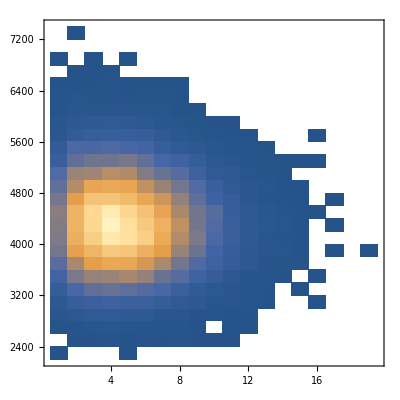

```mathematica
DensityHistogram[Select[#[[1]]>0&][SampleEvent["ER",2,100000]],{20,20}]
```

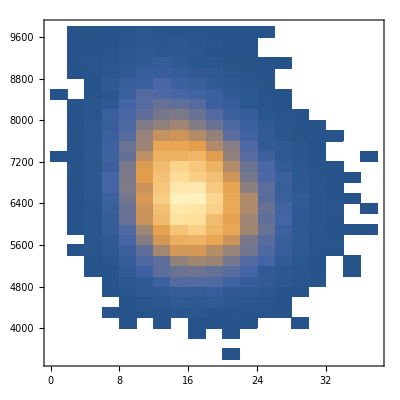

```mathematica
DensityHistogram[Select[#[[1]]>0&][SampleEvent["ER",4,100000]],{20,20}]
```

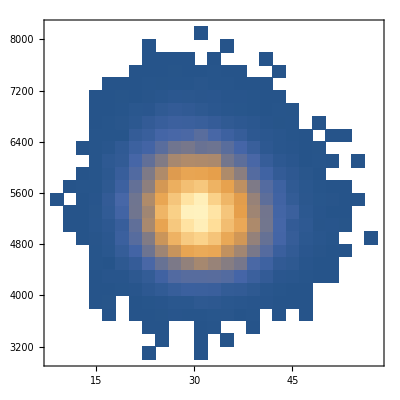

```mathematica
DensityHistogram[Select[#[[1]]>0&][SampleEvent["NR",26,100000]],{20,20}]
```